1.

1.

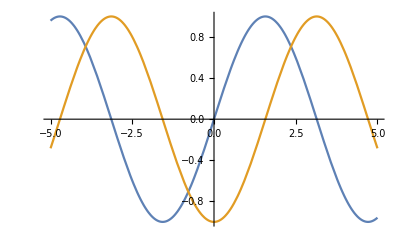

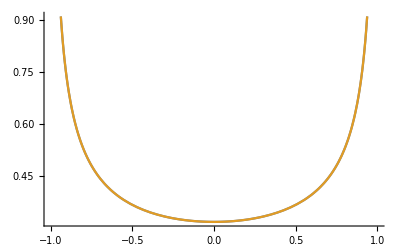

```mathematica
(* Hilbert Transform function definition *)
HilbertTransform[f_,u_,t_]:=Module[{fp=FourierParameters->{1,-1},x},InverseFourierTransform[-I (2 HeavisideTheta[x]-1) FourierTransform[f,u,x,fp],x,t,fp]]

(* Input function and support *)
fy = Sin[t];
supp1=-Pi/2;
supp2=Pi/2;

(* Assume uniform distribution across support *)
fx=1/(supp2-supp1);

(* Find Hilbert Transform of function *)
fyh =Simplify[ComplexExpand[ HilbertTransform[fy,t,t]]];

(* Calculate CDF and PDF of the function and its Hilbert Transform *)
ty=Simplify[t/.First[Solve[y==fy,t]]];
ty = ty[[1]];
tyh=Simplify[t/.First[Solve[yh==fyh,t]]];
tyh=tyh[[1]];

cdfy=Integrate[fx,{w,0,ty}];
pdfy=Abs[D[cdfy,y]];
cdfyh=Integrate[fx,{w,0,tyh}];
pdfyh=Abs[D[cdfyh,yh]];

ymin=First[FindMinimum[fy,{t,supp1,supp2}]];
ymax=First[FindMaximum[fy,{t,supp1,supp2}]];
yhmin=First[FindMinimum[fyh,{t,supp1,supp2}]];
yhmax=First[FindMaximum[fyh,{t,supp1,supp2}]];

(* Check that AUC = 1*)
Integrate[pdfy,{y,ymin,ymax}]
Integrate[pdfyh,{yh,ymin,ymax}]

(* Plot the function and its transform, along with their PDFs *)
Plot[{fy,fyh},{t,ymin*5,ymax*5}]
Plot[{pdfy,pdfyh/.yh->y},{y,ymin,ymax}]
```

```mathematica
(* Find differential entropies *)
entropyy=-Integrate[pdfy*Log2[pdfy],{y,ymin,ymax}]
entropyyh=-Integrate[pdfyh*Log2[pdfyh],{yh,yhmin,yhmax}]
```

0.651496

0.651496

```mathematica
(* If y and yh are independent *)
pdfyyhindependent = pdfy*pdfyh;
Plot3D[pdfyyhindependent,{y,ymin,ymax},{yh,ymin,ymax}]
```

-Graphics3D-

```mathematica
(* Find joint entropy and mutual information if the two are independent *)
entropyyyhindependent=-Integrate[Integrate[pdfyyhindependent*Log2[pdfyyhindependent],{yh,yhmin,yhmax}],{y,ymin,ymax}]
mutualinfoindependent = entropyyyhindependent-entropyy-entropyyh
```